```mathematica
Clear["Global`*"]
```

```mathematica
(*定义常微分方程组*)
eqns={
-c *U[x]-q *U[x]^3+(3/2) q *U[x] V[x]-(q/4)* U''[x] ,
-c *V[x]+(3/4) q* V[x]^2-3 q *U[x]^2 V[x]+(3 q/4)* (U'[x])^2+(3 q/2) *U[x] U''[x]-(1/4) q *V''[x] 
}/.{U-> Function[x,Subscript[a, 0] +Subscript[a, 1]*P[x]+Subscript[b, 1]*P[x]^(-1)], V-> Function[x,Subscript[c, 0] +Subscript[c, 1]*P[x]+Subscript[c, 2]*P[x]^2+Subscript[d, 1]*P[x]^(-1)+Subscript[d, 2]*P[x]^(-2)]};
```

```mathematica
Clear[Subscript[r, 0],Subscript[r, 1],Subscript[r, 2],Subscript[r, 3],Subscript[r, 4]]
```

参考文献：Analytical soliton solutions for cubic-quartic perturbations of the Lakshmanan-Porsezian-Daniel equation using the modified extended tanh function method (have typo!)

Optical soliton perturbation with Kudryashov’s generalized law of refractive index and generalized nonlocal laws by improved modified extended tanh method

约束方程：




情况2

```mathematica
(*情况1(无解)： r0=r1=r3=0; *)
(*情况2(有解)： r0=r2^2/(4*r4);r1=r3=0; *)
(*情况3(无解)： r0=r1=r2=0; *)
(*情况4(有解，复杂)： r0=r1=0; *)
(*情况5(有解)： r1=r3=0; *)
 Subscript[r, 0]=Subscript[r, 2]^2/(4*Subscript[r, 4]);Subscript[r, 1]=Subscript[r, 3]=0;
SubEqns = eqns/.{P'[x] ->Sqrt[Subscript[r, 0]+Subscript[r, 1]*P[x]+Subscript[r, 2]*P[x]^2+-Subscript[r, 3]*P[x]^3 + Subscript[r, 4]*P[x]^4 ]}/.{P''[x]->(1/2)*(Subscript[r, 1] + 2*Subscript[r, 2]*P[x] + 3*Subscript[r, 3]*P[x]^2 + 4*Subscript[r, 4]*P[x]^3)}/.{P[x]->P}
```

{-c (a_0+P a_1+b_1/P)-q (a_0+P a_1+b_1/P)^3+3/2 q (a_0+P a_1+b_1/P) (c_0+P c_1+P^2 c_2+d_1/P+d_2/P^2)-1/4 q (1/2 a_1 (2 P r_2+4 P^3 r_4)-(b_1 (2 P r_2+4 P^3 r_4))/(2 P^2)+(2 b_1 (P^2 r_2+r_2^2/(4 r_4)+P^4 r_4))/P^3),-c (c_0+P c_1+P^2 c_2+d_1/P+d_2/P^2)-3 q (a_0+P a_1+b_1/P)^2 (c_0+P c_1+P^2 c_2+d_1/P+d_2/P^2)+3/4 q (c_0+P c_1+P^2 c_2+d_1/P+d_2/P^2)^2+3/4 q (a_1 √(P^2 r_2+r_2^2/(4 r_4)+P^4 r_4)-(b_1 √(P^2 r_2+r_2^2/(4 r_4)+P^4 r_4))/P^2)^2+3/2 q (a_0+P a_1+b_1/P) (1/2 a_1 (2 P r_2+4 P^3 r_4)-(b_1 (2 P r_2+4 P^3 r_4))/(2 P^2)+(2 b_1 (P^2 r_2+r_2^2/(4 r_4)+P^4 r_4))/P^3)-1/4 q (1/2 c_1 (2 P r_2+4 P^3 r_4)+P c_2 (2 P r_2+4 P^3 r_4)-(d_1 (2 P r_2+4 P^3 r_4))/(2 P^2)-(d_2 (2 P r_2+4 P^3 r_4))/P^3+2 c_2 (P^2 r_2+r_2^2/(4 r_4)+P^4 r_4)+(2 d_1 (P^2 r_2+r_2^2/(4 r_4)+P^4 r_4))/P^3+(6 d_2 (P^2 r_2+r_2^2/(4 r_4)+P^4 r_4))/P^4)}

```mathematica
(*每一项乘上P四次方，变为正次的多项式*)
expandedEqns=Expand[SubEqns*P^4]
```

{-c P^4 a_0-P^4 q a_0^3-c P^5 a_1-3 P^5 q a_0^2 a_1-3 P^6 q a_0 a_1^2-P^7 q a_1^3-c P^3 b_1-3 P^3 q a_0^2 b_1-6 P^4 q a_0 a_1 b_1-3 P^5 q a_1^2 b_1-3 P^2 q a_0 b_1^2-3 P^3 q a_1 b_1^2-P q b_1^3+3/2 P^4 q a_0 c_0+3/2 P^5 q a_1 c_0+3/2 P^3 q b_1 c_0+3/2 P^5 q a_0 c_1+3/2 P^6 q a_1 c_1+3/2 P^4 q b_1 c_1+3/2 P^6 q a_0 c_2+3/2 P^7 q a_1 c_2+3/2 P^5 q b_1 c_2+3/2 P^3 q a_0 d_1+3/2 P^4 q a_1 d_1+3/2 P^2 q b_1 d_1+3/2 P^2 q a_0 d_2+3/2 P^3 q a_1 d_2+3/2 P q b_1 d_2-1/4 P^5 q a_1 r_2-1/4 P^3 q b_1 r_2-(P q b_1 r_2^2)/(8 r_4)-1/2 P^7 q a_1 r_4,-c P^4 c_0-3 P^4 q a_0^2 c_0-6 P^5 q a_0 a_1 c_0-3 P^6 q a_1^2 c_0-6 P^3 q a_0 b_1 c_0-6 P^4 q a_1 b_1 c_0-3 P^2 q b_1^2 c_0+3/4 P^4 q c_0^2-c P^5 c_1-3 P^5 q a_0^2 c_1-6 P^6 q a_0 a_1 c_1-3 P^7 q a_1^2 c_1-6 P^4 q a_0 b_1 c_1-6 P^5 q a_1 b_1 c_1-3 P^3 q b_1^2 c_1+3/2 P^5 q c_0 c_1+3/4 P^6 q c_1^2-c P^6 c_2-3 P^6 q a_0^2 c_2-6 P^7 q a_0 a_1 c_2-3 P^8 q a_1^2 c_2-6 P^5 q a_0 b_1 c_2-6 P^6 q a_1 b_1 c_2-3 P^4 q b_1^2 c_2+3/2 P^6 q c_0 c_2+3/2 P^7 q c_1 c_2+3/4 P^8 q c_2^2-c P^3 d_1-3 P^3 q a_0^2 d_1-6 P^4 q a_0 a_1 d_1-3 P^5 q a_1^2 d_1-6 P^2 q a_0 b_1 d_1-6 P^3 q a_1 b_1 d_1-3 P q b_1^2 d_1+3/2 P^3 q c_0 d_1+3/2 P^4 q c_1 d_1+3/2 P^5 q c_2 d_1+3/4 P^2 q d_1^2-c P^2 d_2-3 P^2 q a_0^2 d_2-6 P^3 q a_0 a_1 d_2-3 P^4 q a_1^2 d_2-6 P q a_0 b_1 d_2-6 P^2 q a_1 b_1 d_2-3 q b_1^2 d_2+3/2 P^2 q c_0 d_2+3/2 P^3 q c_1 d_2+3/2 P^4 q c_2 d_2+3/2 P q d_1 d_2+(3 q d_2^2)/4+3/2 P^5 q a_0 a_1 r_2+9/4 P^6 q a_1^2 r_2+3/2 P^3 q a_0 b_1 r_2+3/2 P^4 q a_1 b_1 r_2+9/4 P^2 q b_1^2 r_2-1/4 P^5 q c_1 r_2-P^6 q c_2 r_2-1/4 P^3 q d_1 r_2-P^2 q d_2 r_2+(3 P^4 q a_1^2 r_2^2)/(16 r_4)+(3 P q a_0 b_1 r_2^2)/(4 r_4)+(3 P^2 q a_1 b_1 r_2^2)/(8 r_4)+(15 q b_1^2 r_2^2)/(16 r_4)-(P^4 q c_2 r_2^2)/(8 r_4)-(P q d_1 r_2^2)/(8 r_4)-(3 q d_2 r_2^2)/(8 r_4)+3 P^7 q a_0 a_1 r_4+15/4 P^8 q a_1^2 r_4+3/2 P^6 q a_1 b_1 r_4+3/4 P^4 q b_1^2 r_4-1/2 P^7 q c_1 r_4-3/2 P^8 q c_2 r_4-1/2 P^4 q d_2 r_4}

```mathematica
(* P 的各个次幂*)
coeffEqns=Flatten[CoefficientList[expandedEqns,P]];
(*列出方程组*)
eqnList=Thread[coeffEqns==0]
```

{True,-q b_1^3+3/2 q b_1 d_2-(q b_1 r_2^2)/(8 r_4)==0,-3 q a_0 b_1^2+3/2 q b_1 d_1+3/2 q a_0 d_2==0,-c b_1-3 q a_0^2 b_1-3 q a_1 b_1^2+3/2 q b_1 c_0+3/2 q a_0 d_1+3/2 q a_1 d_2-1/4 q b_1 r_2==0,-c a_0-q a_0^3-6 q a_0 a_1 b_1+3/2 q a_0 c_0+3/2 q b_1 c_1+3/2 q a_1 d_1==0,-c a_1-3 q a_0^2 a_1-3 q a_1^2 b_1+3/2 q a_1 c_0+3/2 q a_0 c_1+3/2 q b_1 c_2-1/4 q a_1 r_2==0,-3 q a_0 a_1^2+3/2 q a_1 c_1+3/2 q a_0 c_2==0,-q a_1^3+3/2 q a_1 c_2-1/2 q a_1 r_4==0,-3 q b_1^2 d_2+(3 q d_2^2)/4+(15 q b_1^2 r_2^2)/(16 r_4)-(3 q d_2 r_2^2)/(8 r_4)==0,-3 q b_1^2 d_1-6 q a_0 b_1 d_2+3/2 q d_1 d_2+(3 q a_0 b_1 r_2^2)/(4 r_4)-(q d_1 r_2^2)/(8 r_4)==0,-3 q b_1^2 c_0-6 q a_0 b_1 d_1+(3 q d_1^2)/4-c d_2-3 q a_0^2 d_2-6 q a_1 b_1 d_2+3/2 q c_0 d_2+9/4 q b_1^2 r_2-q d_2 r_2+(3 q a_1 b_1 r_2^2)/(8 r_4)==0,-6 q a_0 b_1 c_0-3 q b_1^2 c_1-c d_1-3 q a_0^2 d_1-6 q a_1 b_1 d_1+3/2 q c_0 d_1-6 q a_0 a_1 d_2+3/2 q c_1 d_2+3/2 q a_0 b_1 r_2-1/4 q d_1 r_2==0,-c c_0-3 q a_0^2 c_0-6 q a_1 b_1 c_0+(3 q c_0^2)/4-6 q a_0 b_1 c_1-3 q b_1^2 c_2-6 q a_0 a_1 d_1+3/2 q c_1 d_1-3 q a_1^2 d_2+3/2 q c_2 d_2+3/2 q a_1 b_1 r_2+(3 q a_1^2 r_2^2)/(16 r_4)-(q c_2 r_2^2)/(8 r_4)+3/4 q b_1^2 r_4-1/2 q d_2 r_4==0,-6 q a_0 a_1 c_0-c c_1-3 q a_0^2 c_1-6 q a_1 b_1 c_1+3/2 q c_0 c_1-6 q a_0 b_1 c_2-3 q a_1^2 d_1+3/2 q c_2 d_1+3/2 q a_0 a_1 r_2-1/4 q c_1 r_2==0,-3 q a_1^2 c_0-6 q a_0 a_1 c_1+(3 q c_1^2)/4-c c_2-3 q a_0^2 c_2-6 q a_1 b_1 c_2+3/2 q c_0 c_2+9/4 q a_1^2 r_2-q c_2 r_2+3/2 q a_1 b_1 r_4==0,-3 q a_1^2 c_1-6 q a_0 a_1 c_2+3/2 q c_1 c_2+3 q a_0 a_1 r_4-1/2 q c_1 r_4==0,-3 q a_1^2 c_2+(3 q c_2^2)/4+15/4 q a_1^2 r_4-3/2 q c_2 r_4==0}

方程组展示

```mathematica
Exponent[expandedEqns,P]
eqnShow = # ==0&/@coeffEqns /.P->ϕ;
allP=Join[Table[Inactivate[ϕ^n,Power],{n,0,7}],Table[Inactivate[ϕ^n,Power],{n,0,8}]];
Grid[Transpose[{allP,eqnShow }]]
```

{7,8}

ϕ^0 | True
ϕ^1 | -q b_1^3+3/2 q b_1 d_2-(q b_1 r_2^2)/(8 r_4)==0
ϕ^2 | -3 q a_0 b_1^2+3/2 q b_1 d_1+3/2 q a_0 d_2==0
ϕ^3 | -c b_1-3 q a_0^2 b_1-3 q a_1 b_1^2+3/2 q b_1 c_0+3/2 q a_0 d_1+3/2 q a_1 d_2-1/4 q b_1 r_2==0
ϕ^4 | -c a_0-q a_0^3-6 q a_0 a_1 b_1+3/2 q a_0 c_0+3/2 q b_1 c_1+3/2 q a_1 d_1==0
ϕ^5 | -c a_1-3 q a_0^2 a_1-3 q a_1^2 b_1+3/2 q a_1 c_0+3/2 q a_0 c_1+3/2 q b_1 c_2-1/4 q a_1 r_2==0
ϕ^6 | -3 q a_0 a_1^2+3/2 q a_1 c_1+3/2 q a_0 c_2==0
ϕ^7 | -q a_1^3+3/2 q a_1 c_2-1/2 q a_1 r_4==0
ϕ^0 | -3 q b_1^2 d_2+(3 q d_2^2)/4+(15 q b_1^2 r_2^2)/(16 r_4)-(3 q d_2 r_2^2)/(8 r_4)==0
ϕ^1 | -3 q b_1^2 d_1-6 q a_0 b_1 d_2+3/2 q d_1 d_2+(3 q a_0 b_1 r_2^2)/(4 r_4)-(q d_1 r_2^2)/(8 r_4)==0
ϕ^2 | -3 q b_1^2 c_0-6 q a_0 b_1 d_1+(3 q d_1^2)/4-c d_2-3 q a_0^2 d_2-6 q a_1 b_1 d_2+3/2 q c_0 d_2+9/4 q b_1^2 r_2-q d_2 r_2+(3 q a_1 b_1 r_2^2)/(8 r_4)==0
ϕ^3 | -6 q a_0 b_1 c_0-3 q b_1^2 c_1-c d_1-3 q a_0^2 d_1-6 q a_1 b_1 d_1+3/2 q c_0 d_1-6 q a_0 a_1 d_2+3/2 q c_1 d_2+3/2 q a_0 b_1 r_2-1/4 q d_1 r_2==0
ϕ^4 | -c c_0-3 q a_0^2 c_0-6 q a_1 b_1 c_0+(3 q c_0^2)/4-6 q a_0 b_1 c_1-3 q b_1^2 c_2-6 q a_0 a_1 d_1+3/2 q c_1 d_1-3 q a_1^2 d_2+3/2 q c_2 d_2+3/2 q a_1 b_1 r_2+(3 q a_1^2 r_2^2)/(16 r_4)-(q c_2 r_2^2)/(8 r_4)+3/4 q b_1^2 r_4-1/2 q d_2 r_4==0
ϕ^5 | -6 q a_0 a_1 c_0-c c_1-3 q a_0^2 c_1-6 q a_1 b_1 c_1+3/2 q c_0 c_1-6 q a_0 b_1 c_2-3 q a_1^2 d_1+3/2 q c_2 d_1+3/2 q a_0 a_1 r_2-1/4 q c_1 r_2==0
ϕ^6 | -3 q a_1^2 c_0-6 q a_0 a_1 c_1+(3 q c_1^2)/4-c c_2-3 q a_0^2 c_2-6 q a_1 b_1 c_2+3/2 q c_0 c_2+9/4 q a_1^2 r_2-q c_2 r_2+3/2 q a_1 b_1 r_4==0
ϕ^7 | -3 q a_1^2 c_1-6 q a_0 a_1 c_2+3/2 q c_1 c_2+3 q a_0 a_1 r_4-1/2 q c_1 r_4==0
ϕ^8 | -3 q a_1^2 c_2+(3 q c_2^2)/4+15/4 q a_1^2 r_4-3/2 q c_2 r_4==0

```mathematica
(*解代数决定方程组*)
Clear[c]
(*约束条件为：如果这几项全部都为零就排除，不显示 ,AnyTrue[{Subscript[a, 1],Subscript[b, 1],Subscript[c, 1],Subscript[c, 2],Subscript[d, 1],Subscript[d, 2]},#!=0&]*)
addConstraints={q!=0,Not[(Subscript[a, 1]==0&&Subscript[b, 1]==0)||(Subscript[c, 1]==0&&Subscript[c, 2]==0&&Subscript[d, 1]==0&&Subscript[d, 2]==0)]};
solutions=Solve[Join[eqnList,addConstraints],{Subscript[r, 2],Subscript[r, 4],Subscript[a, 0],Subscript[a, 1],Subscript[b, 1],Subscript[c, 0],Subscript[c, 1],Subscript[c, 2],Subscript[d, 1],Subscript[d, 2]}];
solutions//Column
```

Solve::svars: 方程可能无法给出所有 " solve " 变量的解.

{r_2→(2 c)/q,r_4→c^2/(q^2 b_1^2),a_0→0,a_1→0,c_0→c/q,c_1→0,c_2→0,d_1→0,d_2→b_1^2}
{r_2→(8 c)/q,r_4→(4 c^2)/(q^2 b_1^2),a_0→0,a_1→0,c_0→(2 c)/q,c_1→0,c_2→0,d_1→0,d_2→2 b_1^2}
{r_2→(2 c)/q,r_4→c^2/(4 q^2 b_1^2),a_0→-(ⅈ √c)/(2 √q),a_1→0,c_0→c/(2 q),c_1→0,c_2→0,d_1→0,d_2→2 b_1^2}
{r_2→(2 c)/q,r_4→c^2/(4 q^2 b_1^2),a_0→(ⅈ √c)/(2 √q),a_1→0,c_0→c/(2 q),c_1→0,c_2→0,d_1→0,d_2→2 b_1^2}
{r_2→c/(2 q),r_4→c^2/(16 q^2 b_1^2),a_0→0,a_1→-c/(4 q b_1),c_0→c/(2 q),c_1→0,c_2→c^2/(16 q^2 b_1^2),d_1→0,d_2→b_1^2}
{r_2→(2 c)/q,r_4→c^2/(4 q^2 b_1^2),a_0→0,a_1→-c/(4 q b_1),c_0→c/q,c_1→0,c_2→c^2/(8 q^2 b_1^2),d_1→0,d_2→2 b_1^2}
{r_2→c/(2 q),r_4→c^2/(64 q^2 b_1^2),a_0→-(ⅈ √c)/(2 √q),a_1→-c/(16 q b_1),c_0→c/(4 q),c_1→0,c_2→c^2/(128 q^2 b_1^2),d_1→0,d_2→2 b_1^2}
{r_2→c/(2 q),r_4→c^2/(64 q^2 b_1^2),a_0→(ⅈ √c)/(2 √q),a_1→-c/(16 q b_1),c_0→c/(4 q),c_1→0,c_2→c^2/(128 q^2 b_1^2),d_1→0,d_2→2 b_1^2}
{r_2→(2 c)/q,r_4→a_1^2,a_0→0,b_1→0,c_0→c/q,c_1→0,c_2→a_1^2,d_1→0,d_2→0}
{r_2→(8 c)/q,r_4→4 a_1^2,a_0→0,b_1→0,c_0→(2 c)/q,c_1→0,c_2→2 a_1^2,d_1→0,d_2→0}
{r_2→(2 c)/q,r_4→4 a_1^2,a_0→-(ⅈ √c)/(2 √q),b_1→0,c_0→c/(2 q),c_1→0,c_2→2 a_1^2,d_1→0,d_2→0}
{r_2→(2 c)/q,r_4→4 a_1^2,a_0→(ⅈ √c)/(2 √q),b_1→0,c_0→c/(2 q),c_1→0,c_2→2 a_1^2,d_1→0,d_2→0}

```mathematica
FullSimplify[D[Sqrt[r0+r1*P[x]+r2*P[x]^2+r3*P[x]^3 + r4*P[x]^4 ],x]/.{P'[x] ->Sqrt[r0+r1*P[x]+r2*P[x]^2+r3*P[x]^3 + r4*P[x]^4 ]}]
```

P[x] (r2+2 r4 P[x]^2)

-Graphics-

```mathematica
(*solutions = DeleteCases[solutionsRaw,_?(ContainsAll[#,{Subscript[a, 0]->0,Subscript[a, 1]->0,Subscript[b, 1]->0}]&)] ;*)
solNice = Flatten[GatherBy[solutions,First[#]&],1];
(*solNice = solNice[[2;; ;;2]]; (*按偶数选,减少解的数列,从这里面继续选*)

solNice=solNice[[{3,5,7}]];
*)
(*solNice=Map[Append[#,Subscript[b, 1]->1]&,solNice[[{1,4}]]/.Subscript[b, 1]->1]~Join~{ Append[solNice[[5]]/.Subscript[a, 1]->1,Subscript[a, 1]->1]}*)
solNice=Map[Append[#,Subscript[b, 1]->1]&,solNice[[{1,4}]]/.Subscript[b, 1]->1]~Join~{ Append[solNice[[5]]/.Subscript[a, 1]->1,Subscript[a, 1]->1]}
solNice//Column
```

{{r_2→(2 c)/q,r_4→c^2/q^2,a_0→0,a_1→0,c_0→c/q,c_1→0,c_2→0,d_1→0,d_2→1,b_1→1},{r_2→(2 c)/q,r_4→c^2/(4 q^2),a_0→0,a_1→-c/(4 q),c_0→c/q,c_1→0,c_2→c^2/(8 q^2),d_1→0,d_2→2,b_1→1},{r_2→(2 c)/q,r_4→1,a_0→0,b_1→0,c_0→c/q,c_1→0,c_2→1,d_1→0,d_2→0,a_1→1}}

{r_2→(2 c)/q,r_4→c^2/q^2,a_0→0,a_1→0,c_0→c/q,c_1→0,c_2→0,d_1→0,d_2→1,b_1→1}
{r_2→(2 c)/q,r_4→c^2/(4 q^2),a_0→0,a_1→-c/(4 q),c_0→c/q,c_1→0,c_2→c^2/(8 q^2),d_1→0,d_2→2,b_1→1}
{r_2→(2 c)/q,r_4→1,a_0→0,b_1→0,c_0→c/q,c_1→0,c_2→1,d_1→0,d_2→0,a_1→1}

```mathematica
odeList =P[z]->Sqrt[Subscript[r, 2]/(2*Subscript[r, 4])]*Tan[Sqrt[Subscript[r, 2]/2]*z]/.solNice
```

{P[z]→√(q/c) Tan[√(c/q) z],P[z]→2 √(q/c) Tan[√(c/q) z],P[z]→√(c/q) Tan[√(c/q) z]}

```mathematica
vNicer= MapThread[(Subscript[c, 0] +Subscript[c, 1]*P[z]+Subscript[c, 2]*P[z]^2+Subscript[d, 1]*P[z]^(-1)+Subscript[d, 2]*P[z]^(-2)/. #1/. #2/. z->(x-c*t))&,{solNice,odeList}];
uNicer = MapThread[(Subscript[a, 0] +Subscript[a, 1]*P[z]+Subscript[b, 1]*P[z]^(-1)/. #1/. #2/. z->(x-c*t))&,{solNice ,odeList}];
Grid[Transpose[{Subscript[r, 2]/.solNice,MapIndexed[Subscript[u, First[#2+35]]->#1&,uNicer],MapIndexed[Subscript[v, First[#2+35]]->#1&//TrigToExp,vNicer]}]]
```

k | u_36→Cot[√(c/q) (-c t+x)]/(√(q/c)) | v_36→c/q+(c Cot[√(c/q) (-c t+x)]^2)/q
k | u_37→Cot[√(c/q) (-c t+x)]/(2 √(q/c))-(c √(q/c) Tan[√(c/q) (-c t+x)])/(2 q) | v_37→c/q+(c Cot[√(c/q) (-c t+x)]^2)/(2 q)+(c Tan[√(c/q) (-c t+x)]^2)/(2 q)
k | u_38→√(c/q) Tan[√(c/q) (-c t+x)] | v_38→c/q+(c Tan[√(c/q) (-c t+x)]^2)/q

-Graphics3D-

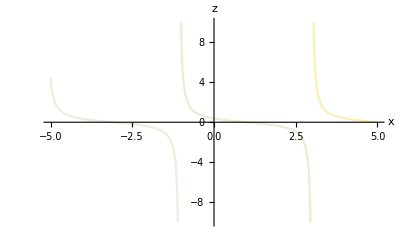

```mathematica
paraC=1.5;paraQ=10;
xValuesCot=Table[Sqrt[c/q] (-c t+x)==n*Pi,{n,-10,10}];
xValuesTan=Table[Sqrt[c/q] (-c t+x)==n*Pi/2,{n,-10,10}];
setting1={ClippingStyle->None,
Exclusions->Flatten[{xValuesCot/. {q->paraQ,c->paraC},xValuesTan/. {q->paraQ,c->paraC}}],ColorFunction->(ColorData["TemperatureMap"][Rescale[#3,{-3,3},{0,1}]]&),
ColorFunctionScaling->False,
PlotPoints->70
};

f[x_,t_]:=Cot[√(c/q) (-c t+x)]/(2 √(q/c))-(c √(q/c) Tan[√(c/q) (-c t+x)])/(2 q)/.{q->paraQ,c->paraC};
g[x_,t_]:=c/q+(c Cot[√(c/q) (-c t+x)]^2)/(2 q)+(c Tan[√(c/q) (-c t+x)]^2)/(2 q)/.{q->paraQ,c->paraC}
Plot3D[f[x,t],{x,-5,5},{t,0,3},Evaluate[setting1],AxesLabel->{"x","t","u_10"," "}]
Plot[f[x,2],{x,-5,5},AxesLabel->{x,z},ColorFunction-> "TemperatureMap",PlotRange->{-10,10},Exclusions->Flatten[{xValuesCot/. {q->paraQ,c->paraC,t->2},xValuesTan/. {q->paraQ,c->paraC,t->2}}]]
```

```mathematica
CoolColor[ z_ ] :=RGBColor[z,1-z,1];
```

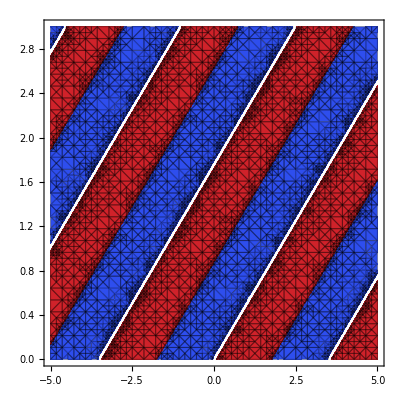

```mathematica
ContourPlot[f[x,t],{x,-5,5},{t,0,3},Mesh->All,PlotRange->All,
ColorFunction->"TemperatureMap"]
```

```mathematica
GraphicsRow[
{
Plot3D[f[x,t],{x,-5,5},{t,0,3},Evaluate[setting1],

AxesLabel->{"x","t","u_37"," "}],
Plot3D[g[x,t],{x,-5,5},{t,0,3},Evaluate[setting1],
AxesLabel->{"x","t","v_37"," "}]
},ImageSize->800]
```

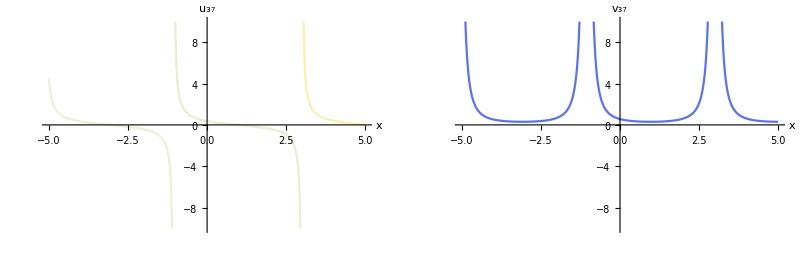

```mathematica
GraphicsRow[
{
Plot[f[x,2],{x,-5,5},AxesLabel->{x,Subscript[u, 37]},ColorFunction-> "TemperatureMap",PlotRange->{-10,10},Exclusions->Flatten[{xValuesCot/. {q->paraQ,c->paraC,t->2},xValuesTan/. {q->paraQ,c->paraC,t->2}}]],
Plot[g[x,2],{x,-5,5},AxesLabel->{x,Subscript[v, 37]},ColorFunction-> "TemperatureMap",PlotRange->{-10,10},Exclusions->Flatten[{xValuesCot/. {q->paraQ,c->paraC,t->2},xValuesTan/. {q->paraQ,c->paraC,t->2}}]]
},
ImageSize->800]
```

```mathematica
(*原始偏微分方程*)
Peqns={D[u[x,t],t]-3 q u[x,t]^2 D[u[x,t],x]+(3/2) q D[(u[x,t] v[x,t]),x]-(1/4) q D[u[x,t],{x,3}]==0,D[v[x,t],t]+(3/2) q v[x,t] D[v[x,t],x]-3 q D[(u[x,t]^2 v[x,t]),x]+3 q D[u[x,t],x] D[u[x,t],{x,2}]+(3/2) q u[x,t] D[u[x,t],{x,3}]-(1/4) q D[v[x,t],{x,3}]==0};
(*批量验证，虽然笨拙代码，但很快*)
Map[
(Peqns/. 
{u->Function[{x,t},uNicer[[#]]],
v->Function[{x,t},vNicer[[#]]]
}
)&,{Table[i,{i,Length[uNicer]}]}
]
```

{{{0,0,0}==0,{0,0,0}==0}}